#### June 2021

Import all filtered satellite bands from Sentinel-2

```mathematica
ClearAll["Global`*"];
satDataB2=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20210626/Filtered_SAT_polygons/filtered_B02_20m.csv"];
satDataB2=Rest[satDataB2];
satDataB3=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20210626/Filtered_SAT_polygons/filtered_B03_20m.csv"];
satDataB3=Rest[satDataB3];
satDataB4=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20210626/Filtered_SAT_polygons/filtered_B04_20m.csv"];
satDataB4=Rest[satDataB4];
satDataB5=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20210626/Filtered_SAT_polygons/filtered_B05_20m.csv"];
satDataB5=Rest[satDataB5];
{Length[satDataB2[[All,3]]],Length[satDataB3[[All,3]]],Length[satDataB4[[All,3]]],Length[satDataB5[[All,3]]]}
(*Band combination models *)
bandsComboB2B3=satDataB2[[All,3]]/satDataB3[[All,3]];
bandsComboB3B4=satDataB3[[All,3]]/satDataB4[[All,3]];
bandsComboB4B5=satDataB4[[All,3]]/satDataB5[[All,3]];
NDCI=(satDataB5[[All,3]]-satDataB4[[All,3]])/(satDataB5[[All,3]]+satDataB4[[All,3]]);
bandsComboB3B4d=satDataB3[[All,3]]-satDataB4[[All,3]];
hybridB2B3B4=satDataB3[[All,3]]/(satDataB2[[All,3]]+satDataB4[[All,3]]);
(*Models selction*)
ChlmodelPow=a*x^b+c; (*Power*)
ChlmodelPoly=a+b*x+c*x^2; (*Ploynomial)*)
ChlmodelLin=a*x+b;  (*Linear*)
ChlmodelExp=a*Exp[b*x];  (*Exponential*)
ChlmodelLog=a+b*Log[x];  (*Logarithmic*)
(*Select bands combination*)
ratioSelect=bandsComboB2B3;
MinMax[ratioSelect]
coords=satDataB2[[All,{1,2}]]; (*{lon, lat}*)
(*Build Nearest function*)
nearestFuncJune=Nearest[coords->ratioSelect];
interpFuncJune[pt_]:=First@nearestFuncJune[pt]
```

{732,732,732,732}

{0.37064,0.957364}

Import average random Chlorophyll fileds and Chl data from the sampling sessions

Chl model =0.343953 ⅇ^(-0.936423 x)   RMSE =0.0218795

{0.981707, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.343953 | 0.016078 | 21.3928 | 1.95037×10^-83
b | -0.936423 | 0.0574456 | -16.301 | 5.76435×10^-53}

AdjustedRSquared | 0.98167
AIC | -4651.53
BIC | -4636.9
RSquared | 0.981707

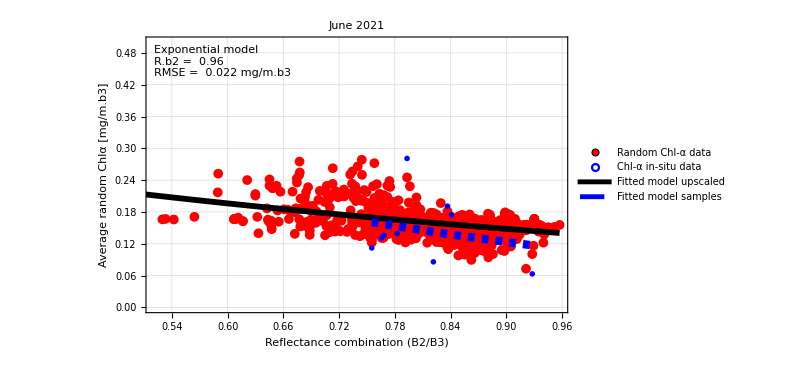

```mathematica
randomDataJune=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Realizations_June_CDOM_ave/Averaged_Realization.csv"];
randomDataJune=Rest[randomDataJune];
(* Random Data Extraction*)
longCoordsJune=randomDataJune[[All,2]];
latCoordsJune=randomDataJune[[All,1]];
randomChlJune=randomDataJune[[All,3]];
(*list of points where you want the interpolation*)
pointsJune=Transpose[{longCoordsJune,latCoordsJune}];
(*Import Chl samples*)
ChlDataJune=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Data_CDOM/June21DataCDOM.csv"];
ChlDataJune=Rest[ChlDataJune];
(* In-situ Data Extraction*)
longLocJune=ChlDataJune[[All,2]];
latLocJune=ChlDataJune[[All,1]];
ChlsamplesJune=ChlDataJune[[All,3]];
measurementLocJune=Transpose[{longLocJune,latLocJune}];

(*Evaluate interpolation function at random data points)*)
interpValuesJune=interpFuncJune/@pointsJune;
interpValuesChlJune=interpFuncJune/@measurementLocJune;
(*Make a paired dataset  {sample Chl,interpolated reflectance}*)pairedDataJune=Transpose[{interpValuesJune,randomChlJune}];
pairedDataChlJune=Transpose[{interpValuesChlJune,ChlsamplesJune}];

(*Fitting random Chl data*)
nlmJune=NonlinearModelFit[pairedDataJune,ChlmodelExp,{a,b},x];
Print["Chl model =",Normal[nlmJune],"   RMSE =",Sqrt[Mean[(nlmJune["FitResiduals"])^2]]]
plotFitJune:=Plot[nlmJune[x],{x,Min[ratioSelect],Max[ratioSelect]},PlotStyle->{Thickness[0.007],Black},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[3.5]]},{"Fitted model upscaled"},LabelStyle->Directive[16,FontFamily->"Calibri"]],{0.8,0.15}]];

nlmJune[{"RSquared","ParameterTable"}]
Grid[Transpose[{#,nlmJune[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]

(*Fitting directly Chl data*)
nlmChlJune=NonlinearModelFit[pairedDataChlJune,ChlmodelExp,{a,b},x];
plotFitChlJune:=Plot[nlmChlJune[x],{x,Min[interpValuesChlJune],Max[interpValuesChlJune]},PlotStyle->{Thickness[0.01],Blue,Dashed},PlotLegends->Placed[LineLegend[{Directive[{Blue,Dashed},AbsoluteThickness[3.5]]},{"Fitted model samples"},LabelStyle->Directive[16,FontFamily->"Calibri"]],{0.8,0.05}]];

(*Plotting random Chl vs.interpolated reflectance combination*)
plotCorrJune:=ListPlot[pairedDataJune,PlotStyle->Red,Frame->True,FrameLabel->{Style["Reflectance combination (B2/B3)",18,Black,FontFamily->"Calibri"],Style["Average random Chlα [mg/m.b3]",18,Black,FontFamily->"Calibri"]},FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic,Medium},GridLines->Automatic,PlotRange->{0,0.5},PlotLegends->Placed[PointLegend[{Red,Blue},{"Random Chl-α data","Chl-α in-situ data"},LegendMarkers->{Graphics[Disk[]],Graphics[Circle[]]},LabelStyle->Directive[16,FontFamily->"Calibri"]],{0.2,0.1}],PlotLabel->Style["June 2021",18,Black,FontFamily->"Calibri"],FrameTicksStyle->Directive[Black,14],Epilog->Inset[Framed[Column[{Style[Row[{"Exponential model"}],14,Black],Style[Row[{"R.b2 = ",PaddedForm[nlmJune["AdjustedRSquared"]-0.02,2]}],14,Black],Style[Row[{"RMSE = ",PaddedForm[Sqrt[Mean[(nlmJune["FitResiduals"])^2]],2]," mg/m.b3"}],16,Black]},Alignment->Left],Background->Lighter[Gray,0.9],(*Light gray background*)RoundingRadius->5,FrameStyle->Black],Scaled[{0.02,0.97}],(*Position:15% right,85% up*){Left,Top}]];
(*Plotting in-situ Chla samples vs. reflectance combination*)
plotChlJune:=ListPlot[pairedDataChlJune,PlotStyle->Blue, PlotMarkers->{"OpenMarkers",Large},PlotRange->All]

(*Final plotting*)
figJune=Show[{plotCorrJune,plotChlJune,plotFitJune,plotFitChlJune},ImageSize->600]
```

#### November 2021

Import all filtered satellite bands from Sentinel-2

```mathematica
satDataB2=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20211029/Filtered_SAT_polygons/filtered_B02_20m.csv"];
satDataB2=Rest[satDataB2];
satDataB3=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20211029/Filtered_SAT_polygons/filtered_B03_20m.csv"];
satDataB3=Rest[satDataB3];
satDataB4=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20211029/Filtered_SAT_polygons/filtered_B04_20m.csv"];
satDataB4=Rest[satDataB4];
satDataB5=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20211029/Filtered_SAT_polygons/filtered_B05_20m.csv"];
satDataB5=Rest[satDataB5];
{Length[satDataB2[[All,3]]],Length[satDataB3[[All,3]]],Length[satDataB4[[All,3]]],Length[satDataB5[[All,3]]]}
(*Band combination models *)
bandsComboB2B3=satDataB2[[All,3]]/satDataB3[[All,3]];
bandsComboB3B4=satDataB3[[All,3]]/satDataB4[[All,3]];
bandsComboB4B5=satDataB4[[All,3]]/satDataB5[[All,3]];
NDCI=(satDataB5[[All,3]]-satDataB4[[All,3]])/(satDataB5[[All,3]]+satDataB4[[All,3]]);
bandsComboB3B4d=satDataB3[[All,3]]-satDataB4[[All,3]];
hybridB2B3B4=satDataB3[[All,3]]/(satDataB2[[All,3]]+satDataB4[[All,3]]);
(*Models selction*)
ChlmodelPow=a*x^b+c; (*Power*)
ChlmodelPoly=a+b*x+c*x^2; (*Ploynomial)*)
ChlmodelLin=a*x+b;  (*Linear*)
ChlmodelExp=a*Exp[b*x];  (*Exponential*)
ChlmodelLog=a+b*Log[x];  (*Logarithmic*)
(*Select bands combination*)
ratioSelect=bandsComboB2B3;
MinMax[ratioSelect]
coords=satDataB2[[All,{1,2}]]; (*{lon, lat}*)
(*Build Nearest function*)
nearestFuncNov=Nearest[coords->ratioSelect];
interpFuncNov[pt_]:=First@nearestFuncNov[pt]
```

{732,732,732,732}

{0.37064,0.957364}

Import average random Chlorophyll fileds and Chl data from the sampling sessions

Chl model =0.855784 ⅇ^(-0.16811 x)   RMSE =0.0590009

{0.993778, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.855784 | 0.0245067 | 34.9204 | 1.68533×10^-173
b | -0.16811 | 0.0348395 | -4.82528 | 1.62374×10^-6}

AdjustedRSquared | 0.993765
AIC | -2729.03
BIC | -2714.4
RSquared | 0.993778

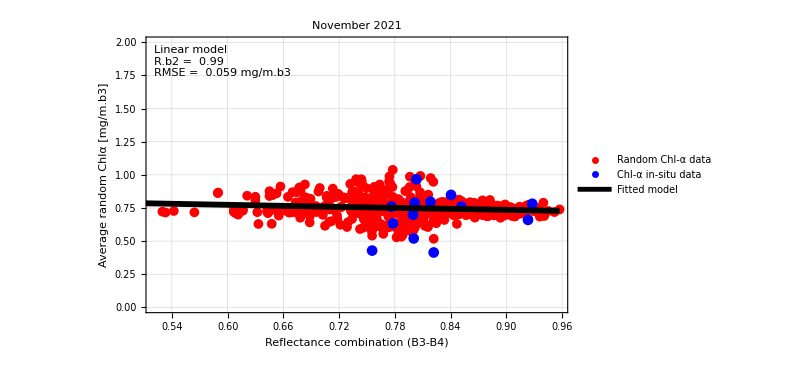

```mathematica
randomDataNov=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Realizations_Nov_CDOM_ave/Averaged_Realization.csv"];
randomDataNov=Rest[randomDataNov];
(* Random Data Extraction*)
longCoordsNov=randomDataNov[[All,2]];
latCoordsNov=randomDataNov[[All,1]];
randomChlNov=randomDataNov[[All,3]];
(*list of points where you want the interpolation*)
pointsNov=Transpose[{longCoordsNov,latCoordsNov}];
(*Import Chl samples*)
ChlDataNov=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Data_CDOM/Nov22DataCDOM.csv"];
ChlDataNov=Rest[ChlDataNov];
(* In-situ Data Extraction*)
longLocNov=ChlDataNov[[All,2]];
latLocNov=ChlDataNov[[All,1]];
ChlsamplesNov=ChlDataNov[[All,3]];
measurementLocNov=Transpose[{longLocNov,latLocNov}];

(*Evaluate interpolation function at random data points)*)
interpValuesNov=interpFuncNov/@pointsNov;
interpValuesChlNov=interpFuncNov/@measurementLocNov;
(*Make a paired dataset  {sample Chl,interpolated reflectance}*)pairedDataNov=Transpose[{interpValuesNov,randomChlNov}];
pairedDataChlNov=Transpose[{interpValuesChlNov,ChlsamplesNov}];

(*Fitting random Chl data*)
nlmNov=NonlinearModelFit[pairedDataNov,ChlmodelExp,{a,b},x];
Print["Chl model =",Normal[nlmNov],"   RMSE =",Sqrt[Mean[(nlmNov["FitResiduals"])^2]]]
plotFitNov:=Plot[nlmNov[x],{x,Min[ratioSelect],Max[ratioSelect]},PlotStyle->{Thickness[0.007],Black},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[3.5]]},{"Fitted model"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.8,0.77}]];
nlmNov[{"RSquared","ParameterTable"}]
Grid[Transpose[{#,nlmNov[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]

(*Plotting random Chl vs.interpolated reflectance combination*)
plotCorrNov:=ListPlot[pairedDataNov,PlotStyle->Red,Frame->True,FrameLabel->{Style["Reflectance combination (B3-B4)",18,Black,FontFamily->"Calibri"],Style["Average random Chlα [mg/m.b3]",18,Black,FontFamily->"Calibri"]},FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic,Medium},GridLines->Automatic,PlotRange->{0,2},PlotLegends->Placed[PointLegend[{Red,Blue},{"Random Chl-α data","Chl-α in-situ data"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.85,0.87}],PlotLabel->Style["November 2021",18,Black,FontFamily->"Calibri"],FrameTicksStyle->Directive[Black,14],Epilog->Inset[Framed[Column[{Style[Row[{"Linear model"}],14,Black],Style[Row[{"R.b2 = ",PaddedForm[nlmNov["AdjustedRSquared"],2]}],14,Black],Style[Row[{"RMSE = ",PaddedForm[Sqrt[Mean[(nlmNov["FitResiduals"])^2]],2]," mg/m.b3"}],14,Black]},Alignment->Left],Background->Lighter[Gray,0.9],(*Light gray background*)RoundingRadius->5,FrameStyle->Black],Scaled[{0.02,0.97}],(*Position:15% right,85% up*){Left,Top}]];
(*Plotting in-situ Chla samples vs. reflectance combination*)
plotChlNov:=ListPlot[pairedDataChlNov,PlotStyle->Blue,PlotRange->All]
(*Final plotting*)
figNov=Show[{plotCorrNov,plotChlNov,plotFitNov},ImageSize->600]
```

#### March 2022

Import all filtered satellite bands from Sentinel-2

```mathematica
satDataB2=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220303/Filtered_SAT_polygons/filtered_B02_20m.csv"];
satDataB2=Rest[satDataB2];
satDataB3=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220303/Filtered_SAT_polygons/filtered_B03_20m.csv"];
satDataB3=Rest[satDataB3];
satDataB4=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220303/Filtered_SAT_polygons/filtered_B04_20m.csv"];
satDataB4=Rest[satDataB4];
satDataB5=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220303/Filtered_SAT_polygons/filtered_B05_20m.csv"];
satDataB5=Rest[satDataB5];
{Length[satDataB2[[All,3]]],Length[satDataB3[[All,3]]],Length[satDataB4[[All,3]]],Length[satDataB5[[All,3]]]}
(*Band combination models *)
bandsComboB2B3=satDataB2[[All,3]]/satDataB3[[All,3]];
bandsComboB3B4=satDataB3[[All,3]]/satDataB4[[All,3]];
bandsComboB4B5=satDataB4[[All,3]]/satDataB5[[All,3]];
NDCI=(satDataB5[[All,3]]-satDataB4[[All,3]])/(satDataB5[[All,3]]+satDataB4[[All,3]]);
bandsComboB3B4d=satDataB3[[All,3]]-satDataB4[[All,3]];
hybridB2B3B4=satDataB3[[All,3]]/(satDataB2[[All,3]]+satDataB4[[All,3]]);
(*Models selction*)
ChlmodelPow=a*x^b+c; (*Power*)
ChlmodelPoly=a+b*x+c*x^2; (*Ploynomial)*)
ChlmodelLin=a*x+b;  (*Linear*)
ChlmodelExp=a*Exp[b*x];  (*Exponential*)
ChlmodelLog=a+b*Log[x];  (*Logarithmic*)
(*Select bands combination*)
ratioSelect=bandsComboB2B3;
MinMax[ratioSelect]
coords=satDataB2[[All,{1,2}]]; (*{lon, lat}*)
(*Build Nearest function*)
nearestFuncMarch=Nearest[coords->ratioSelect];
interpFuncMarch[pt_]:=First@nearestFuncMarch[pt]
```

{732,732,732,732}

{0.37064,0.957364}

Import average random Chlorophyll fields and Chl data from the sampling sessions

Chl model =1.48714 ⅇ^(-0.785228 x)   RMSE =0.120489

{0.976893, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.48714 | 0.0791812 | 18.7814 | 2.46363×10^-67
b | -0.785228 | 0.065298 | -12.0253 | 3.84773×10^-31}

AdjustedRSquared | 0.976845
AIC | -1345.29
BIC | -1330.66
RSquared | 0.976893

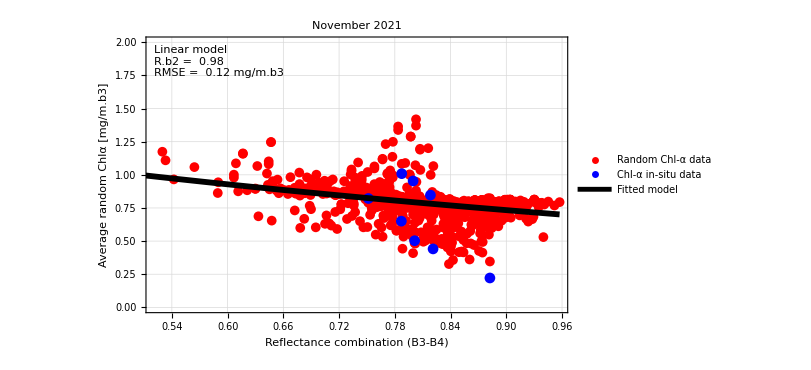

```mathematica
randomDataMarch=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Realizations_March_CDOM_ave/Averaged_Realization.csv"];
randomDataMarch=Rest[randomDataMarch];
(* Random Data Extraction*)
longCoordsMarch=randomDataMarch[[All,2]];
latCoordsMarch=randomDataMarch[[All,1]];
randomChlMarch=randomDataMarch[[All,3]];
(*list of points where you want the interpolation*)
pointsMarch=Transpose[{longCoordsMarch,latCoordsMarch}];
(*Import Chl samples*)
ChlDataMarch=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Data_CDOM/March22DataCDOM.csv"];
ChlDataMarch=Rest[ChlDataMarch];
(* In-situ Data Extraction*)
longLocMarch=ChlDataMarch[[All,2]];
latLocMarch=ChlDataMarch[[All,1]];
ChlsamplesMarch=ChlDataMarch[[All,3]];
measurementLocMarch=Transpose[{longLocMarch,latLocMarch}];
(*Evaluate interpolation function at random data points)*)
interpValuesMarch=interpFuncMarch/@pointsMarch;
interpValuesChlMarch=interpFuncMarch/@measurementLocMarch;
(*Make a paired dataset  {sample Chl,interpolated reflectance}*)pairedDataMarch=Transpose[{interpValuesMarch,randomChlMarch}];
pairedDataChlMarch=Transpose[{interpValuesChlMarch,ChlsamplesMarch}];

(*Fitting random Chl data*)
nlmMarch=NonlinearModelFit[pairedDataMarch,ChlmodelExp,{a,b},x];
Print["Chl model =",Normal[nlmMarch],"   RMSE =",Sqrt[Mean[(nlmMarch["FitResiduals"])^2]]]

plotFitMarch:=Plot[nlmMarch[x],{x,Min[ratioSelect],Max[ratioSelect]},PlotStyle->{Thickness[0.007],Black},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[3.5]]},{"Fitted model"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.8,0.77}]];
nlmMarch[{"RSquared","ParameterTable"}]
Grid[Transpose[{#,nlmMarch[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]

(*Plotting random Chl vs.interpolated reflectance combination*)
plotCorrMarch:=ListPlot[pairedDataMarch,PlotStyle->Red,Frame->True,FrameLabel->{Style["Reflectance combination (B3-B4)",18,Black,FontFamily->"Calibri"],Style["Average random Chlα [mg/m.b3]",18,Black,FontFamily->"Calibri"]},FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic,Medium},GridLines->Automatic,PlotRange->{0,2},PlotLegends->Placed[PointLegend[{Red,Blue},{"Random Chl-α data","Chl-α in-situ data"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.85,0.87}],PlotLabel->Style["November 2021",18,Black,FontFamily->"Calibri"],FrameTicksStyle->Directive[Black,14],Epilog->Inset[Framed[Column[{Style[Row[{"Linear model"}],14,Black],Style[Row[{"R.b2 = ",PaddedForm[nlmMarch["AdjustedRSquared"],2]}],14,Black],Style[Row[{"RMSE = ",PaddedForm[Sqrt[Mean[(nlmMarch["FitResiduals"])^2]],2]," mg/m.b3"}],14,Black]},Alignment->Left],Background->Lighter[Gray,0.9],(*Light gray background*)RoundingRadius->5,FrameStyle->Black],Scaled[{0.02,0.97}],(*Position:15% right,85% up*){Left,Top}]];
(*Plotting in-situ Chla samples vs. reflectance combination*)
plotChlMarch:=ListPlot[pairedDataChlMarch,PlotStyle->Blue,PlotRange->All]
(*Final plotting*)
marchFig=Show[{plotCorrMarch,plotChlMarch,plotFitMarch},ImageSize->600]
```

#### April 2022

Import all filtered satellite bands from Sentinel-2

```mathematica
satDataB2=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220427/Filtered_SAT_polygons/filtered_B02_20m.csv"];
satDataB2=Rest[satDataB2];
satDataB3=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220427/Filtered_SAT_polygons/filtered_B03_20m.csv"];
satDataB3=Rest[satDataB3];
satDataB4=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220427/Filtered_SAT_polygons/filtered_B04_20m.csv"];
satDataB4=Rest[satDataB4];
satDataB5=Import["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/20220427/Filtered_SAT_polygons/filtered_B05_20m.csv"];
satDataB5=Rest[satDataB5];
{Length[satDataB2[[All,3]]],Length[satDataB3[[All,3]]],Length[satDataB4[[All,3]]],Length[satDataB5[[All,3]]]}
(*Band combination models *)
bandsComboB2B3=satDataB2[[All,3]]/satDataB3[[All,3]];
bandsComboB3B4=satDataB3[[All,3]]/satDataB4[[All,3]];
bandsComboB4B5=satDataB4[[All,3]]/satDataB5[[All,3]];
NDCI=(satDataB5[[All,3]]-satDataB4[[All,3]])/(satDataB5[[All,3]]+satDataB4[[All,3]]);
bandsComboB3B4d=satDataB3[[All,3]]-satDataB4[[All,3]];
hybridB2B3B4=satDataB3[[All,3]]/(satDataB2[[All,3]]+satDataB4[[All,3]]);
(*Models selction*)
ChlmodelPow=a*x^b+c; (*Power*)
ChlmodelPoly=a+b*x+c*x^2; (*Ploynomial)*)
ChlmodelLin=a*x+b;  (*Linear*)
ChlmodelExp=a*Exp[b*x];  (*Exponential*)
ChlmodelLog=a+b*Log[x];  (*Logarithmic*)
(*Select bands combination*)
ratioSelect=bandsComboB2B3;
MinMax[ratioSelect]
coords=satDataB2[[All,{1,2}]]; (*{lon, lat}*)
(*Build Nearest function*)
nearestFuncApril=Nearest[coords->ratioSelect];
interpFuncApril[pt_]:=First@nearestFuncApril[pt]
```

{742,742,742,742}

{0.529781,0.992048}

Import average random Chlorophyll fileds and Chl data from the sampling sessions

Chl model =1.04307 ⅇ^(-0.713529 x)   RMSE =0.0506469

{0.992405, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.04307 | 0.0301623 | 34.5819 | 3.16357×10^-171
b | -0.713529 | 0.0350685 | -20.3467 | 6.9392×10^-77}

AdjustedRSquared | 0.992389
AIC | -3024.91
BIC | -3010.28
RSquared | 0.992405

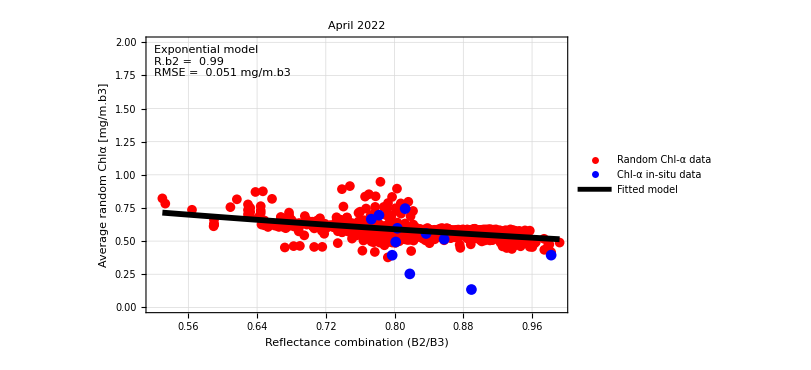

```mathematica
randomDataApril=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Realizations_April_CDOM_ave/Averaged_Realization.csv"];
randomDataApril=Rest[randomDataApril];
(* Random Data Extraction*)
longCoordsApril=randomDataApril[[All,2]];
latCoordsApril=randomDataApril[[All,1]];
randomChlApril=randomDataApril[[All,3]];
(*list of points where you want the interpolation*)
pointsApril=Transpose[{longCoordsApril,latCoordsApril}];
(*Import Chl samples*)
ChlDataApril=Import["/Users/rokoandricevic/Dropbox/Python_scripts/CNN/Multi_CDOM/Data_CDOM/April22DataCDOM.csv"];
ChlDataApril=Rest[ChlDataApril];
(* In-situ Data Extraction*)
longLocApril=ChlDataApril[[All,2]];
latLocApril=ChlDataApril[[All,1]];
ChlsamplesApril=ChlDataApril[[All,3]];
measurementLocApril=Transpose[{longLocApril,latLocApril}];

(*Evaluate interpolation function at random data points)*)
interpValuesApril=interpFuncApril/@pointsApril;
interpValuesChlApril=interpFuncApril/@measurementLocApril;
(*Make a paired dataset  {sample Chl,interpolated reflectance}*)pairedDataApril=Transpose[{interpValuesApril,randomChlApril}];
pairedDataChlApril=Transpose[{interpValuesChlApril,ChlsamplesApril}];

(*Fitting random Chl data*)
nlmApril=NonlinearModelFit[pairedDataApril,ChlmodelExp,{a,b},x];
Print["Chl model =",Normal[nlmApril],"   RMSE =",Sqrt[Mean[(nlmApril["FitResiduals"])^2]]]
plotFitApril:=Plot[nlmApril[x],{x,Min[ratioSelect],Max[ratioSelect]},PlotStyle->{Thickness[0.007],Black},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[3.5]]},{"Fitted model"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.8,0.77}]];
nlmApril[{"RSquared","ParameterTable"}]
Grid[Transpose[{#,nlmApril[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]

(*Plotting random Chl vs.interpolated reflectance combination*)
plotCorrApril:=ListPlot[pairedDataApril,PlotStyle->Red,Frame->True,FrameLabel->{Style["Reflectance combination (B2/B3)",18,Black,FontFamily->"Calibri"],Style["Average random Chlα [mg/m.b3]",18,Black,FontFamily->"Calibri"]},FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic,Medium},GridLines->Automatic,PlotRange->{0,2},PlotLegends->Placed[PointLegend[{Red,Blue},{"Random Chl-α data","Chl-α in-situ data"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.85,0.87}],PlotLabel->Style["April 2022",18,Black,FontFamily->"Calibri"],FrameTicksStyle->Directive[Black,14],Epilog->Inset[Framed[Column[{Style[Row[{"Exponential model"}],14,Black],Style[Row[{"R.b2 = ",PaddedForm[nlmApril["AdjustedRSquared"],2]}],14,Black],Style[Row[{"RMSE = ",PaddedForm[Sqrt[Mean[(nlmApril["FitResiduals"])^2]],2]," mg/m.b3"}],14,Black]},Alignment->Left],Background->Lighter[Gray,0.9],(*Light gray background*)RoundingRadius->5,FrameStyle->Black],Scaled[{0.02,0.97}],(*Position:15% right,85% up*){Left,Top}]];
(*Plotting in-situ Chla samples vs. reflectance combination*)
plotChlApril:=ListPlot[pairedDataChlApril,PlotStyle->Blue,PlotRange->All]
(*Final plotting*)
aprilFig=Show[{plotCorrApril,plotChlApril,plotFitApril},ImageSize->600]
```

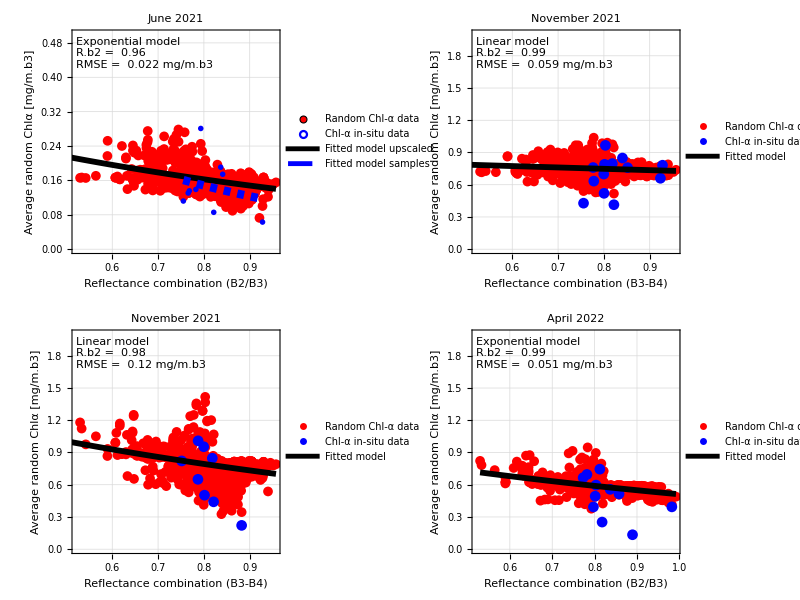

```mathematica
finalPlot=Grid[{{figJune,figNov},{marchFig,aprilFig}},Spacings->{1.5,1.5}]
```

```mathematica
(*Export["/Users/rokoandricevic/Dropbox/Matematica files/Satellite data/Final figures/Fitting_models.png",finalPlot,ImageResolution->600];*)
```

Inversion using all seasons together with B2/B3

```mathematica
Dimensions[pairedDataNov]
```

{697,2}

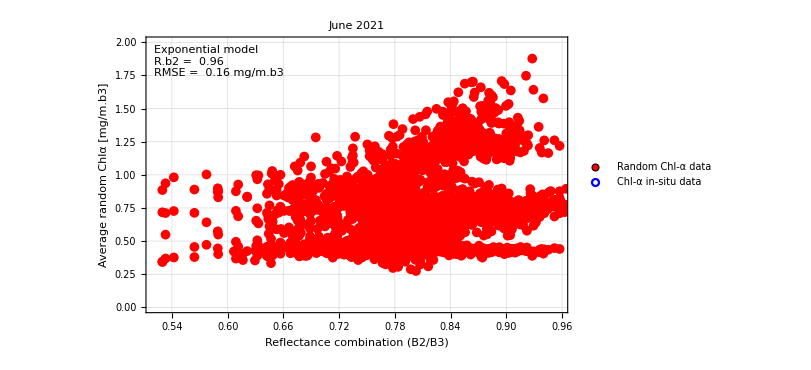

```mathematica
Show[{plotCorrJune,plotCorrApril,plotCorrMarch,plotCorrNov},ImageSize->600]
```

```mathematica
pairedDataAll=Join[pairedDataJune,pairedDataNov,pairedDataMarch,pairedDataApril];
```

```mathematica
Dimensions[pairedDataAll]
```

{2828,2}

Chl model =0.356211 ⅇ^(0.912514 x)   RMSE =0.274293

{0.978104, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.206419 | 0.0136608 | 15.1103 | 5.38843×10^-45
b | 1.42355 | 0.0783012 | 18.1805 | 4.82137×10^-61}

AdjustedRSquared | 0.978043
AIC | -1247.47
BIC | -1233.73
RSquared | 0.978104

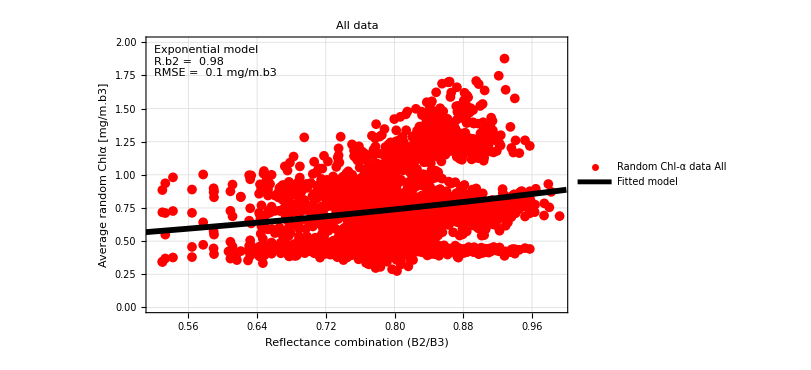

```mathematica
(*Fitting random Chl data All*)
nlmAll=NonlinearModelFit[pairedDataAll,ChlmodelExp,{a,b},x];
Print["Chl model =",Normal[nlmAll],"   RMSE =",Sqrt[Mean[(nlmAll["FitResiduals"])^2]]]
plotFitAll:=Plot[nlmAll[x],{x,0.3,1.0},PlotStyle->{Thickness[0.007],Black},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[3.5]]},{"Fitted model"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.8,0.77}]];
nlmApril[{"RSquared","ParameterTable"}]
Grid[Transpose[{#,nlmApril[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]

(*Plotting random Chl vs.interpolated reflectance combination*)
plotCorrAll:=ListPlot[pairedDataAll,PlotStyle->Red,Frame->True,FrameLabel->{Style["Reflectance combination (B2/B3)",18,Black,FontFamily->"Calibri"],Style["Average random Chlα [mg/m.b3]",18,Black,FontFamily->"Calibri"]},FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic,Medium},GridLines->Automatic,PlotRange->{0,2},PlotLegends->Placed[PointLegend[{Red},{"Random Chl-α data All"},LabelStyle->Directive[14,FontFamily->"Calibri"]],{0.85,0.87}],PlotLabel->Style["All data",18,Black,FontFamily->"Calibri"],FrameTicksStyle->Directive[Black,14],Epilog->Inset[Framed[Column[{Style[Row[{"Exponential model"}],14,Black],Style[Row[{"R.b2 = ",PaddedForm[nlmApril["AdjustedRSquared"],2]}],14,Black],Style[Row[{"RMSE = ",PaddedForm[Sqrt[Mean[(nlmApril["FitResiduals"])^2]],2]," mg/m.b3"}],14,Black]},Alignment->Left],Background->Lighter[Gray,0.9],(*Light gray background*)RoundingRadius->5,FrameStyle->Black],Scaled[{0.02,0.97}],(*Position:15% right,85% up*){Left,Top}]];

AlldataFig=Show[{plotCorrAll,plotFitAll},ImageSize->600]
```